```mathematica
(*Вариант 4*)
```

```mathematica
f[x_]=5*Exp[-1/18 x^2+1/3 x-1/2]-2Sin[√x];
```

```mathematica
(*  1.1)n=6  *)
```

```mathematica
A=0;
B=6;
n=6;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 3.03265
1. | 2.32075
2. | 2.75427
3. | 3.02595
4. | 2.9112
5. | 2.43019
6. | 1.75634

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];
```

```mathematica
(*  a)  *)
```

```mathematica
LagrangeInterpolation[dataX_,dataY_,n_]:=∑_(i=1)^n dataY[[i]]*Product[If[i!=j,(x-dataX[[j]])/(dataX[[i]]-dataX[[j]]),1],{j,1,n}];
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=", Ln];
```

Ln(x)=3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6

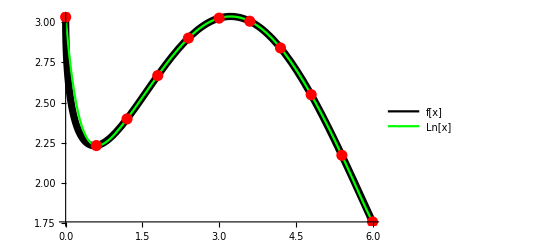

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Ln[x]"}]]
```

```mathematica
(*  б)  *)

Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

3.03265 | -0.711908 | 1.14543 | -1.30727 | 1.08268 | -0.837939 | 0.746473
2.32075 | 0.43352 | -0.161839 | -0.224586 | 0.244742 | -0.0914657 | 0
2.75427 | 0.271681 | -0.386425 | 0.020156 | 0.153277 | 0 | 0
3.02595 | -0.114744 | -0.36627 | 0.173433 | 0 | 0 | 0
2.9112 | -0.481014 | -0.192837 | 0 | 0 | 0 | 0
2.43019 | -0.673851 | 0 | 0 | 0 | 0 | 0
1.75634 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(*  в)  *)
NewtonInterpolationMultilier[dataX_,n_,i_,H_]:=(∏_(k=1)^i ((x-dataX[[n]])/H+k-1))/(i!)
NewtonInterpolationSecondMethod[dataX_,dataY_,deltaTable_,H_,n_]:=dataY[[n]]+∑_(i=1)^(n-1) (NewtonInterpolationMultilier[dataX,n,i,H]*deltaTable[[n-i,i+1]]);
```

```mathematica
Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)="Pn];
```

Pn(x)= (3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6)

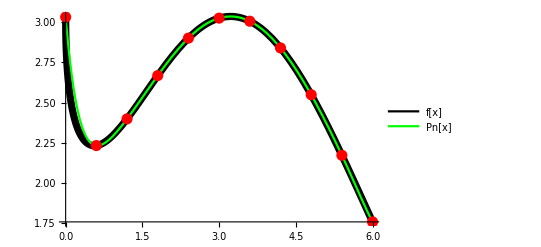

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Pn,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Pn[x]"}]]
```

```mathematica
(*  г)  *)

Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=3.03265-2.28305 x+2.35579 x^2-0.96622 x^3+0.203065 x^4-0.0225344 x^5+0.00103677 x^6

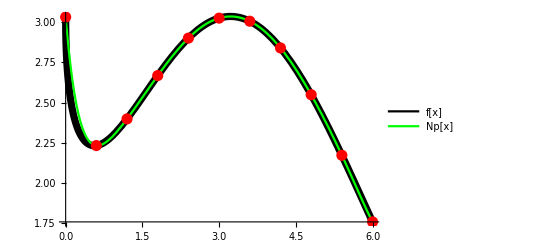

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Np,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Np[x]"}]]
```

```mathematica
(*  д)  *)

Print["f[2.4316]= ",f[2.4316]];
Print["Ln[2.4316]= ",Ln/.x->2.4316];
Print["Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 2.91119

Ln[2.4316]= 2.91645

Pn[2.4316]= 2.91645

Np[2.4316]= 2.91645

```mathematica
(*  е)  *)

Rn=Abs[f[x]-Np];
```

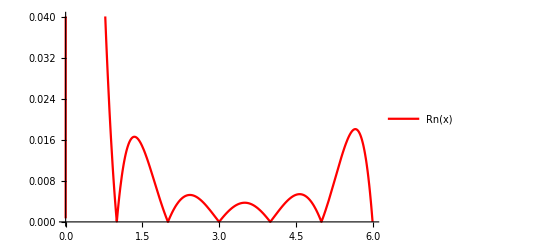

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Red];
Legended[Show[func1],LineLegend[{Red},{"Rn(x)"}]]
```

```mathematica
FindMaximum[{Rn,A<=x<=B},{x,5.5}]
```

{0.018126,{x→5.6632}}

```mathematica
(* 1.2) n = 10 *)
```

```mathematica
n=10;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 3.03265
0.6 | 2.23189
1.2 | 2.39809
1.8 | 2.66786
2.4 | 2.90146
3. | 3.02595
3.6 | 3.0067
4.2 | 2.84029
4.8 | 2.5487
5.4 | 2.17146
6. | 1.75634

```mathematica
dataX=data[[All,1]];
dataY=data[[All,2]];

(*  a)  *)
```

```mathematica
Ln=LagrangeInterpolation[dataX,dataY,n+1]//Simplify;
Print["Ln(x)=",Ln];
```

Ln(x)=3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Ln,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Ln[x]"}]]
```

-Graphics-

```mathematica
(*  б)  *)

Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=dif[i+1,k-1]-dif[i,k-1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData, Frame->All]
```

3.03265 | -0.800764 | 0.966961 | -0.863381 | 0.723619 | -0.656783 | 0.628247 | -0.606797 | 0.586603 | -0.56964 | 0.556376
2.23189 | 0.166198 | 0.10358 | -0.139762 | 0.0668357 | -0.0285367 | 0.0214492 | -0.0201942 | 0.0169631 | -0.0132637 | 0
2.39809 | 0.269778 | -0.0361822 | -0.0729266 | 0.038299 | -0.00708754 | 0.00125503 | -0.0032311 | 0.00369939 | 0 | 0
2.66786 | 0.233595 | -0.109109 | -0.0346276 | 0.0312115 | -0.00583251 | -0.00197607 | 0.000468293 | 0 | 0 | 0
2.90146 | 0.124487 | -0.143736 | -0.0034161 | 0.025379 | -0.00780858 | -0.00150777 | 0 | 0 | 0 | 0
3.02595 | -0.0192497 | -0.147152 | 0.0219628 | 0.0175704 | -0.00931635 | 0 | 0 | 0 | 0 | 0
3.0067 | -0.166402 | -0.12519 | 0.0395332 | 0.00825402 | 0 | 0 | 0 | 0 | 0 | 0
2.84029 | -0.291592 | -0.0856564 | 0.0477872 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.5487 | -0.377248 | -0.0378691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.17146 | -0.415117 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.75634 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
(*  в)  *)

Pn=NewtonInterpolationSecondMethod[dataX,dataY,tableData,H,n+1]//Simplify;
Print["Pn(x)=",Pn];
```

Pn(x)=3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Pn,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Pn[x]"}]]
```

-Graphics-

```mathematica
(*  г)  *)

Np=InterpolatingPolynomial[data,x];
Np=Simplify[Np];
Print["Np(x)=",Np];
```

Np(x)=3.03265-3.77992 x+6.92081 x^2-6.78008 x^3+4.34104 x^4-1.8606 x^5+0.533848 x^6-0.101229 x^7+0.0121725 x^8-0.000840399 x^9+0.0000253567 x^10

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Np,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Np[x]"}]]
```

-Graphics-

```mathematica
(*  д)  *)


Print["f[2.4316]= ",f[2.4316]];
Print[ "Ln[2.4316]= ",Ln/.x->2.4316];
Print[ "Pn[2.4316]= ",Pn/.x->2.4316];
Print["Np[2.4316]= ",Np/.x->2.4316];
```

f[2.4316]= 2.91119

Ln[2.4316]= 2.91122

Pn[2.4316]= 2.91122

Np[2.4316]= 2.91122

```mathematica
(*  е)  *)

Rn=Abs[f[x]-Np];
```

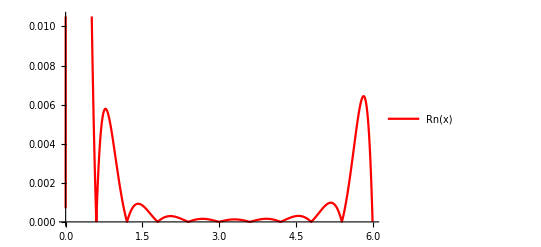

```mathematica
func1=Plot[Rn,{x,0,6},PlotStyle->Red];
Legended[Show[func1],LineLegend[{Red},{"Rn(x)"}]]
```

```mathematica
FindMaximum[{Rn,A<=x<=B},{x,0.1}]
```

{0.221177,{x→0.0572043}}

```mathematica
(*ж) Увеличение количества узлов интерполяции на вышеприведенном графике ведёт к снижению
погрешности интерполяции. Следовательно, количество узлов интерполяции влияет на тончость интерполирования*)


(*2.1)  n=6 *)
n=6;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i];]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.92478 | 1.80879
5.34549 | 2.20803
4.30165 | 2.79879
3. | 3.02595
1.69835 | 2.62201
0.654506 | 2.23608
0.0752163 | 2.56701

```mathematica
(*  а)  *)

DividedDifferenceRecursive[dataX_,dataY_,begin_,end_]:=If[begin+1==end,(dataY[[end]]-dataY[[begin]])/(dataX[[end]]-dataX[[begin]]),(DividedDifferenceRecursive[dataX,dataY,begin+1,end]-DividedDifferenceRecursive[dataX,dataY,begin,end-1])/(dataX[[end]]-dataX[[begin]])]
```

```mathematica
Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,	For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

1.80879 | -0.689177 | -0.0759186 | 0.0311032 | 0.00610376 | -0.000841109 | 0.000763534
2.20803 | -0.565951 | -0.166889 | 0.005306 | 0.0105366 | -0.00530745 | 0
2.79879 | -0.174514 | -0.18624 | -0.0441213 | 0.0385084 | 0 | 0
3.02595 | 0.310326 | -0.0253236 | -0.206874 | 0 | 0 | 0
2.62201 | 0.369722 | 0.579739 | 0 | 0 | 0 | 0
2.23608 | -0.571272 | 0 | 0 | 0 | 0 | 0
2.56701 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
(*  б)  *)
```

```mathematica
NewtonDivDiff[dataX_,dataY_,n_,diff_]:=dataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-dataX[[k]])
```

```mathematica
Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=2.67561-1.57565 x+1.80865 x^2-0.74679 x^3+0.154234 x^4-0.0168179 x^5+0.000763534 x^6

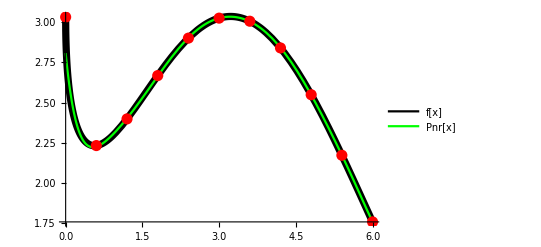

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Pnr[x]"}]]
```

```mathematica
(*  в)  *)

Intf=Interpolation[data];
```

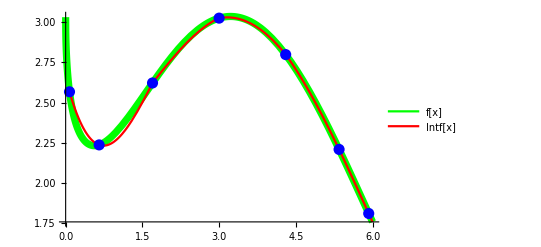

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Red];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Red},{"f[x]","Intf[x]"}]]
```

```mathematica
(*  г)  *)

Print["f[2.4316]= ",f[2.4316]];
Print[ "Pnr[2.4316]= ",Pnr/.x->2.4316];
Print["Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 2.91119

Pnr[2.4316]= 2.92154

Intf[2.4316]= 2.89279

```mathematica
(*  д)  *)

AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},{x,4.5}]
```

{0.00557501,{x→4.84736}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],A<=x<=B},{x,3.5}]
```

{0.0113129,{x→3.61937}}

```mathematica
(*  2.2)  n=10  *)

n=10;
```

```mathematica
For[i=0,i<=n,i++,
Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(A+B)/2+(B-A)/2*Subscript[t, i]]
```

```mathematica
data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

5.96946 | 1.77762
5.7289 | 1.94548
5.26725 | 2.25991
4.62192 | 2.64621
3.8452 | 2.95573
3. | 3.02595
2.1548 | 2.81603
1.37808 | 2.47561
0.732751 | 2.24743
0.271104 | 2.31101
0.0305357 | 2.71581

```mathematica
(*  а)  *)


Array[dif,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,For[i=n,i>=n-k,i--,dif[i,k]="0"]];
For[i=0,i<=n,i++,dif[i,0]=data[[i+1,2]]];
For[k=1,k<=n,k++,For[i=0,i<=n-k,i++,
dif[i,k]=DividedDifferenceRecursive[dataX,dataY,i+1,k+i+1]]];
tableData=Array[dif,{n+1,n+1},{0,0}];
Grid[tableData,Frame->All]
```

1.77762 | -0.69776 | -0.0237267 | 0.0376835 | 0.00118829 | -0.00101426 | -0.0000309145 | 3.7851×10^-6 | 6.90374×10^-6 | -8.26711×10^-6 | 0.0000413112
1.94548 | -0.681098 | -0.0745068 | 0.0351593 | 0.00420011 | -0.000896336 | -0.0000482934 | -0.0000323678 | 0.0000540127 | -0.000253611 | 0
2.25991 | -0.598621 | -0.140736 | 0.0236976 | 0.0074037 | -0.00068622 | 0.000113421 | -0.000327158 | 0.00149918 | 0 | 0
2.64621 | -0.398487 | -0.194465 | 0.00065399 | 0.0100725 | -0.00120053 | 0.00174795 | -0.00817794 | 0 | 0 | 0
2.95573 | -0.0830808 | -0.196078 | -0.0320197 | 0.0147416 | -0.00880553 | 0.039296 | 0 | 0 | 0 | 0
3.02595 | 0.248369 | -0.117082 | -0.0779021 | 0.0462134 | -0.158707 | 0 | 0 | 0 | 0 | 0
2.81603 | 0.438266 | 0.0595418 | -0.204014 | 0.517487 | 0 | 0 | 0 | 0 | 0 | 0
2.47561 | 0.353594 | 0.443842 | -1.30329 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.24743 | -0.137727 | 2.20009 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.31101 | -1.68266 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2.71581 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
differenceResult=Table[dif[i,k],{i,0,n},{k,1,n}];
```

```mathematica
(*  б)  *)

Pnr=NewtonDivDiff[dataX,dataY,n,differenceResult]//Simplify;
Print["Pnr(x)=",Pnr];
```

Pnr(x)=2.80823-3.23075 x+6.91145 x^2-7.84926 x^3+5.67577 x^4-2.65744 x^5+0.810442 x^6-0.159866 x^7+0.0196622 x^8-0.00137027 x^9+0.0000413112 x^10

```mathematica
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Pnr,{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Pnr[x]"}]]
```

-Graphics-

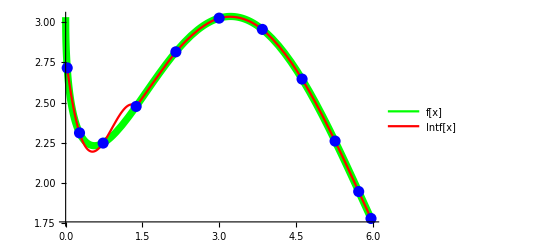

```mathematica
(*  в)  *)

Intf=Interpolation[data];
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.013]}];
func2=Plot[Intf[x],{x,dataX[[n+1]],B},PlotStyle->Red];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Red},{"f[x]","Intf[x]"}]]
```

```mathematica
(*  г)  *)

Print["f[2.4316]= ",f[2.4316]];
Print["Pnr[2.4316]= ",Pnr/.x->2.4316];
Print[ "Intf[2.4316]= ",Intf[2.4316]];
```

f[2.4316]= 2.91119

Pnr[2.4316]= 2.91358

Intf[2.4316]= 2.9085

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
FindMaximum[{AbsPnr[x],A<=x<=B},{x,0.1}]
```

{0.0355287,{x→0.091416}}

```mathematica
(*  д)  *)


AbsIntf[x_]:=Abs[f[x]-Intf[x]];
FindMaximum[{AbsIntf[x],dataX[[n+1]]<=x<=dataX[[1]]},{x,3.4}]
```

```mathematica
{0.00239635559195861,{x->3.4132030306161045}}


(* Исходя из проведенных вычислений и построений можно сделать вывод, что увеличение количества точек уменьшает погрешность интерполирования. Также, величина погрешности зависит от положения точек на графике*)
```

```mathematica
(* 4) *)

n=10;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
Grid[data,Frame->All]
```

0. | 3.03265
0.6 | 2.23189
1.2 | 2.39809
1.8 | 2.66786
2.4 | 2.90146
3. | 3.02595
3.6 | 3.0067
4.2 | 2.84029
4.8 | 2.5487
5.4 | 2.17146
6. | 1.75634

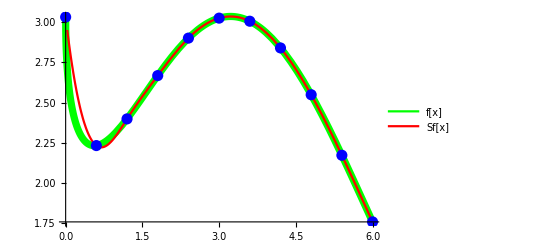

```mathematica
(*  а)  *)

Sf=Interpolation[data,Method->"Spline"];
func1=Plot[f[x],{x,A,B},PlotStyle->{Green,Thickness[0.013]}];
func2=Plot[Sf[x],{x,dataX[[n+1]],B},PlotStyle->Red];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Blue}];
Legended[Show[func1,func2,dots],LineLegend[{Green,Red},{"f[x]","Sf[x]"}]]
```

```mathematica
(*  б)  *)

Print["f[2.4316]= ",f[2.4316]];
Print["Sf[2.4316]= ",Sf[2.4316]];
```

f[2.4316]= 2.91119

Sf[2.4316]= 2.91135

```mathematica
(* 5) *)

n=10;
B=6;
H=B/n;
data=N[Table[{i H,f[i H]},{i,0,n}]];
dataX=data[[All,1]];
dataY=data[[All,2]];
Grid[data,Frame->All]
```

0. | 3.03265
0.6 | 2.23189
1.2 | 2.39809
1.8 | 2.66786
2.4 | 2.90146
3. | 3.02595
3.6 | 3.0067
4.2 | 2.84029
4.8 | 2.5487
5.4 | 2.17146
6. | 1.75634

Q_1(x)=2.85837-0.0866874 x

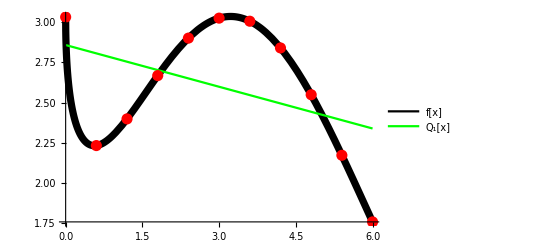

```mathematica
(*  а)  *)

result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,1}]];
polinomialResult=0;
m=1;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 1]=polinomialResult;
Print["Q_1(x)=",Subscript[Q, 1]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Q_1[x]"}]]
```

Q_2(x)=2.45324+0.363462 x-0.0750249 x^2

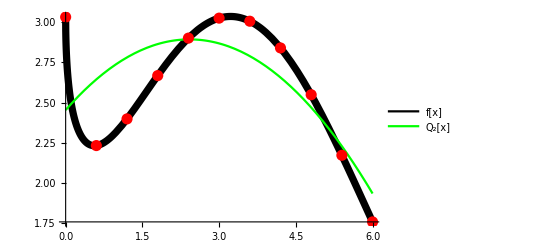

```mathematica
(*  б)  *)

result=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) dataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) dataY[[j]],∑_(j=1)^(n+1) (dataY[[j]]*dataX[[j]]^i)],{i,0,2}]];
polinomialResult=0;
m=2;
k=0;
While[k<=m,polinomialResult=polinomialResult+result[[k+1]]*x^k;k++];
Subscript[Q, 2]=polinomialResult;
Print["Q_2(x)=",Subscript[Q, 2]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Q_2[x]"}]]
```

Q_3(x)=2.77967-0.500976 x+0.302789 x^2-0.0419793 x^3

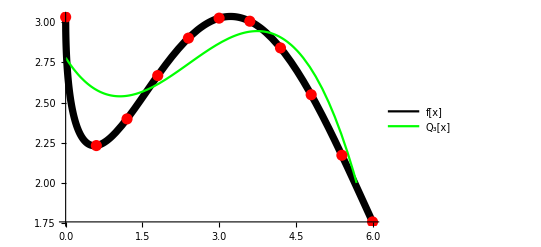

```mathematica
(*  в)  *)

Subscript[Q, 3]=Fit[data,{1,x,x^2,x^3},x];
Print["Q_3(x)=",Subscript[Q, 3]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Q_3[x]"}]]
```

Q_4(x)=2.96666-1.58311 x+1.20456 x^2-0.282453 x^3+0.0200394 x^4

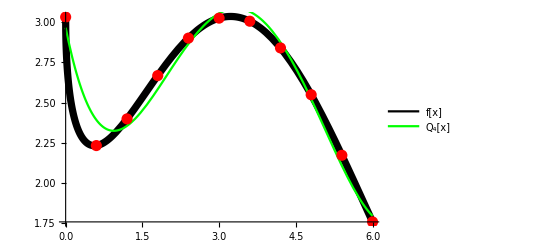

```mathematica
Subscript[Q, 4]=Fit[data,{1,x,x^2,x^3,x^4},x];
Print["Q_4(x)=",Subscript[Q, 4]];
func1=Plot[f[x],{x,A,B},PlotStyle->{Black,Thickness[0.013]}];
func2=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->Green];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func1,func2,dots],LineLegend[{Black,Green},{"f[x]","Q_4[x]"}]]
```

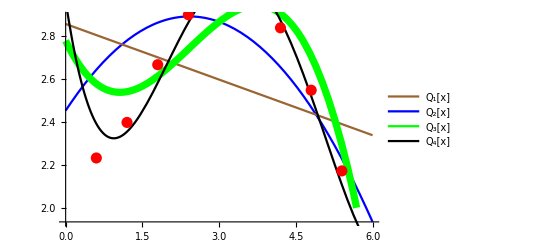

```mathematica
(*  г)  *)


func1=Plot[Subscript[Q, 1],{x,A,B},PlotStyle->Brown];
func2=Plot[Subscript[Q, 2],{x,A,B},PlotStyle->Blue];
func3=Plot[Subscript[Q, 3],{x,A,B},PlotStyle->{Green,Thickness[0.013]}];
func4=Plot[Subscript[Q, 4],{x,A,B},PlotStyle->Black];
dots=ListPlot[data,PlotStyle->{PointSize[0.02],Red}];
Legended[Show[func2,func1,func3,func4,dots],LineLegend[{Brown,Blue,Green,Black},{"Q_1[x]","Q_2[x]","Q_3[x]","Q_4[x]"}]]
```